# Scalar Self Force Tutorial

This tutorial shows how to compute the scalar self force (SSF) for a scalar charge  q in circular orbits around a Schwarzschild black hole. The SSF is defined as  F_α^full(x) =q ∇_α ϕ(x) = ∑_l F_α^((full)l)(x). The tutorials follows https://arxiv.org/pdf/1003.1860.

Load the packages:

```mathematica
<<Teukolsky`
<<SpinWeightedSpheroidalHarmonics`
<<KerrGeodesics`
```

## Time component Ft

Ft
TeukolskyPointParticleMode
SphericalHarmonicY | Function computing the time component of the SSF
Function from the Teukolsky package for the perturbation. We use the extended homogeneous functions:  "ExtendedHomogeneous"->"ℐ","ℋ". 
Function for the spherical harmonics from the SpinWeightedSpheroidalHarmonics package.

Functions used to compute the time component of the SSF. Ft is the  function that make use of the Extended Homogeneous TeukolskyPointParticleMode functions.

Defining the function

```mathematica
Ft[lmax_,r0_,θ_,ϕ_]:=Block[{l,psi,ylm,ω,m,ft,ftsum,ftder,orbit,t, marray, kk=1},
ω=KerrGeoFrequencies[0,r0,0,1][[3]];
orbit=KerrGeoOrbit[0,r0,0,1];

ftsum=0;
For[l=1,l<=lmax, l++,
ft=0; 

For[m=1, m<=l, m++, 
PrintTemporary["(l,m)=(",l,",",m,")"];psi=TeukolskyPointParticleMode[0,l,m,0,0,orbit]["ExtendedHomogeneous"->"ℐ"][r0];ylm=SphericalHarmonicY[l,m,θ,ϕ];
ft = ft +   psi ylm Exp[-I m ω t];
];
ftsum = ftsum+ft;
];

(*the m=0 contributions disappear with the time derivative*)
ftder =D[ftsum,t];
Return[2*Re[ftder//.{t->0}]];
]
```

Evaluating Ft for a specific orbit, summing up to lmax.

```mathematica
lmax= 15; 
r0=14.0`30; 
θ=π/2; 
ϕ=0;
```

```mathematica
Ft[lmax,r0, θ, ϕ]
```

9.236726607294×10^-6

As a comparison, from https://arxiv.org/pdf/1003.1860:  9.23672660e−6

## Radial component Fr

This tutorial shows how to compute the scalar self force (SSF) for a point-particle in circular orbits around a Schwarzschild black hole.  F_α^self = ∑_(l=0)^∞ (F_(α±)^((full)l)- A_(α±) L  - B_α) = ∑_(l=0)^∞ F_α^((reg)l) .

Arps, Arms, Brs | Functions for the regularization parameters. Their output is   (A_(r+),  A_(r-),  B_r) , respectively. 
FrlInf, FrlHor
FrlInfReg, FrlHorReg
FrInfSelf, FrHorSelf
FrRegLTab | Functions giving (F_(r+)^((full)l), F_(r-)^((full)l)) , respectively. 
Functions giving (F_(r+)^((full)l)- A_(r+) L  - B_r, F_(r-)^((full)l)- A_(r-) L  - B_r) 
Functions computing F_r^selfsumming over the (l,m) modes
Functions computing F_r^((reg)l)   giving as output a table with (l,F_r^((reg)l)).

Regularization Parameters

```mathematica
Arps[M_,q_, r_]:= Block[{arp,f,V},
f = 1 - 2 M / r; 
V=  1 + KerrGeoAngularMomentum[0,r,0,1]^2/r^2; 
arp=- q^2 KerrGeoEnergy[0,r,0,1]/ (r^2 f V);
Return[arp];
]

Arms[M_,q_, r_]:= Block[{arm,f,V},
f = 1 - 2 M / r; 
V=  1 + KerrGeoAngularMomentum[0,r,0,1]^2/r^2; 
arm=+ q^2 KerrGeoEnergy[0,r,0,1]/ (r^2 f V);
Return[arm];
]

Brs[M_,q_, r_]:= Block[{br,f,V,E,L,k, EE, w},
f = 1 - 2 M / r; 
L =KerrGeoAngularMomentum[0,r,0,1] ; 
E = KerrGeoEnergy[0,r,0,1];
V=  1 + L^2/r^2; 
w = L^2/(L^2+r^2);
k =EllipticK[w]; 
EE = EllipticE[w]; 
br= (q^2) /r^2 (- 2 E^2 k + (E^2) EE )/(π f V^(3/2));
Return[br];
]
```

Functions for Fr

```mathematica
FrlInf[l_,r0_,θ_,ϕ_]:= Block[{ω,m,orbit,fr, psi,psider,ylm,t,marray,kk=1},ω=KerrGeoFrequencies[0,r0,0,1][[3]];orbit=KerrGeoOrbit[0,r0,0,1];fr=0; 

marray=ConstantArray[0,l];
For[m=1,m<=l,m++,	
marray[[kk]]=m;	
kk = kk+1;
];
marray=Select[marray,EvenQ[#+l]&];

For[m=1, m<=Length[marray], m++,PrintTemporary["(l,m)=","(",l,",",marray[[m]],")"];psi=  TeukolskyPointParticleMode[0,l,marray[[m]],0,0,orbit]["ExtendedHomogeneous"->"ℐ"];psider= psi'[r0];ylm=SphericalHarmonicY[l,marray[[m]],θ,ϕ];fr = fr +   psider ylm Exp[-I marray[[m]] ω 0];
];

(*Do the same thing for the m=0 modes, which are not computed in the previous cycle. If l+m is odd, ylm=0*)
If[EvenQ[l]==True,
m=0;
PrintTemporary["(l,m)=","(",l,",",m,")"];psi=  TeukolskyPointParticleMode[0,l,m,0,0,orbit]["ExtendedHomogeneous"->"ℐ"];psider= psi'[r0];ylm=SphericalHarmonicY[l,m,θ,ϕ];fr = 2*fr +   psider ylm Exp[-I m ω 0];, 
fr = 2*fr;
];
Return[fr//.{t->0}];
]

FrlHor[l_,r0_,θ_,ϕ_]:= Block[{ω,m,orbit,fr, psi,psider,ylm,t},
ω=KerrGeoFrequencies[0,r0,0,1][[3]];orbit=KerrGeoOrbit[0,r0,0,1];fr=0; 
For[m=-l, m<=l, m++, 
PrintTemporary["(l,m)=","(",l,",",m,")"];psi=  TeukolskyPointParticleMode[0,l,m,0,0,orbit]["ExtendedHomogeneous"->"ℋ"];psider= psi'[r0];ylm=SphericalHarmonicY[l,m,θ,ϕ];fr = fr +   psider ylm Exp[-I m ω 0];
];
Return[fr//.{t->0}];
]
```

```mathematica
FrlInfReg[l_,r0_,θ_,ϕ_]:= Block[{frreg,frfull,frsum,fr,rr},
frsum=0;
fr=0;
frfull = FrlInf[l,r0,θ,ϕ];frreg = frfull-Arps[1,1, r0](l+1/2)-Brs[1,1,r0];Return[Re[frreg]];
]

FrlHorReg[l_,r0_,θ_,ϕ_]:= Block[{frreg,frfull,frsum,fr,rr},
frsum=0;
fr=0;
frfull = FrlHor[l,r0,θ,ϕ];frreg = frfull-Arms[1,1, r0](l+1/2)-Brs[1,1,r0];Return[Re[frreg]];
]

FrInfSelf[lmax_,r0_,θ_,ϕ_]:= Block[{frreg,frfull,l,frsum,fr},
frsum=0;
fr=0;
frfull=0;
For[l=0,l<=lmax, l++,
PrintTemporary["l=",l];
frfull = FrlInf[l,r0,θ,ϕ];
frreg = frfull-Arps[1,1, r0](l+1/2)-Brs[1,1,r0];frsum = frsum+frreg;
];
Return[Re[frsum]];
]

FrHorSelf[lmax_,r0_,θ_,ϕ_]:= Block[{frreg,frfull,l,frsum,fr},
frsum=0;
fr=0;
frfull=0;
For[l=0,l<=lmax, l++,
PrintTemporary["l=",l];
frfull = FrlHor[l,r0,θ,ϕ];PrintTemporary["frfull= ", frfull];
frreg = frfull-Arms[1,1, r0](l+1/2)-Brs[1,1,r0];frsum = frsum+frreg;PrintTemporary["frsum= ", frsum];
];
Return[Re[frsum]];
]
```

Example: numerical computation without the tail contribution

Define input parameters

```mathematica
(*It might be necessary to define different values of lmax for r<=7.5. E.g. lmaxlow=39 for r<=7.5 and lmaxhigh=50 for r>=7.5*)
```

```mathematica
(*the input precision of the radius is set to 50. For high modes you might need to increase the input precision. I used If[r0<=75/10,N[r0,450], N[r0,150]]. Here is set to 50 for semplicity.*)
```

```mathematica
lmax=20; 
r0= 14.0`50; 
θ= π/2; 
ϕ=0;
```

```mathematica
FrInfSelf[lmax,r0,θ,ϕ]
```

3.20863032822449516976×10^-7

As a comparison, from https://arxiv.org/pdf/1003.1860:  2.720083e−6. 
The obtained value is much smaller! To compute the tail contribution, let's compute the numerical values again and save the contribution from each l-mode in a table:

```mathematica
FrRegLTab[lmax_,r0_,θ_,ϕ_]:= Block[{frreg,frfull,l,frsum,fr,rr,radius,tab,total,precision},
frsum=0;
fr=0;
frfull=0;
radius= N[r0,50];
Print[radius];
tab= {radius,
ParallelTable[{l,Re[FrlInf[l,radius,θ,ϕ]-Arps[1,1, radius](l+1/2)-Brs[1,1,radius]]},
{l,0,lmax}]};
Return[tab];
]
```

```mathematica
RadiusFrLTab = FrRegLTab[lmax,r0,θ,ϕ];
```

14.

(l,m)=(0,0)

(l,m)=(2,2)

(l,m)=(3,1)

(l,m)=(4,2)

(l,m)=(5,1)

(l,m)=(6,2)

(l,m)=(7,1)

(l,m)=(8,2)

(l,m)=(9,1)

(l,m)=(10,2)

(l,m)=(1,1)

(l,m)=(2,0)

(l,m)=(3,3)

(l,m)=(4,4)

(l,m)=(5,3)

(l,m)=(6,4)

(l,m)=(7,3)

(l,m)=(8,4)

(l,m)=(9,3)

(l,m)=(10,4)

(l,m)=(4,0)

(l,m)=(5,5)

(l,m)=(6,6)

(l,m)=(7,5)

(l,m)=(8,6)

(l,m)=(9,5)

(l,m)=(10,6)

(l,m)=(11,1)

(l,m)=(12,2)

(l,m)=(13,1)

(l,m)=(6,0)

(l,m)=(7,7)

(l,m)=(8,8)

(l,m)=(9,7)

(l,m)=(10,8)

(l,m)=(11,3)

(l,m)=(12,4)

(l,m)=(13,3)

(l,m)=(14,2)

(l,m)=(15,1)

(l,m)=(8,0)

(l,m)=(9,9)

(l,m)=(10,10)

(l,m)=(11,5)

(l,m)=(12,6)

(l,m)=(13,5)

(l,m)=(14,4)

(l,m)=(15,3)

(l,m)=(16,2)

(l,m)=(17,1)

(l,m)=(10,0)

(l,m)=(11,7)

(l,m)=(12,8)

(l,m)=(13,7)

(l,m)=(14,6)

(l,m)=(15,5)

(l,m)=(16,4)

(l,m)=(17,3)

(l,m)=(18,2)

(l,m)=(19,1)

(l,m)=(11,9)

(l,m)=(12,10)

(l,m)=(13,9)

(l,m)=(14,8)

(l,m)=(15,7)

(l,m)=(16,6)

(l,m)=(17,5)

(l,m)=(18,4)

(l,m)=(19,3)

(l,m)=(20,2)

(l,m)=(11,11)

(l,m)=(12,12)

(l,m)=(13,11)

(l,m)=(14,10)

(l,m)=(15,9)

(l,m)=(16,8)

(l,m)=(17,7)

(l,m)=(18,6)

(l,m)=(19,5)

(l,m)=(20,4)

(l,m)=(12,0)

(l,m)=(13,13)

(l,m)=(14,12)

(l,m)=(15,11)

(l,m)=(16,10)

(l,m)=(17,9)

(l,m)=(18,8)

(l,m)=(19,7)

(l,m)=(20,6)

(l,m)=(14,14)

(l,m)=(15,13)

(l,m)=(16,12)

(l,m)=(17,11)

(l,m)=(18,10)

(l,m)=(19,9)

(l,m)=(20,8)

(l,m)=(14,0)

(l,m)=(15,15)

(l,m)=(16,14)

(l,m)=(17,13)

(l,m)=(18,12)

(l,m)=(19,11)

(l,m)=(20,10)

(l,m)=(16,16)

(l,m)=(17,15)

(l,m)=(18,14)

(l,m)=(19,13)

(l,m)=(20,12)

(l,m)=(16,0)

(l,m)=(17,17)

(l,m)=(18,16)

(l,m)=(19,15)

(l,m)=(20,14)

(l,m)=(18,18)

(l,m)=(19,17)

(l,m)=(20,16)

(l,m)=(18,0)

(l,m)=(19,19)

(l,m)=(20,18)

(l,m)=(20,20)

(l,m)=(20,0)

The object built is:

```mathematica
RadiusFrLTab[[1]]
```

14.

```mathematica
SetPrecision[RadiusFrLTab[[2]],5]//MatrixForm
```

(0 | -0.000037155
1. | 9.31×10^-6
2. | 0.000011181
3. | 5.7315×10^-6
4. | 3.0955×10^-6
5. | 1.9086×10^-6
6. | 1.3042×10^-6
7. | 9.5406×10^-7
8. | 7.3089×10^-7
9. | 5.7893×10^-7
10. | 4.7039×10^-7
11. | 3.9001×10^-7
12. | 3.2875×10^-7
13. | 2.8096×10^-7
14. | 2.4293×10^-7
15. | 2.1216×10^-7
16. | 1.8691×10^-7
17. | 1.6593×10^-7
18. | 1.483×10^-7
19. | 1.3335×10^-7
20. | 1.2056×10^-7)

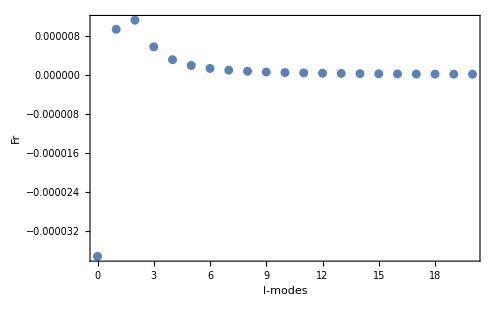

```mathematica
ListPlot[RadiusFrLTab[[2]],Frame->True,FrameStyle->Black, FrameLabel->{Style["l-modes",20,FontFamily->"Latin Modern Roman"],Style["Fr",20,FontFamily->"Latin Modern Roman"]},ImageSize->500,PlotRange->All]
```

In a Log-Log plot it's clear the behaviour of the tail as L^-2 where L=l+1/2.

```mathematica
Lfunction[l_]:=(l+1/2)^-2
```

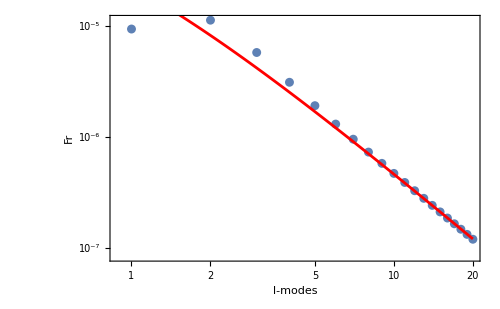

```mathematica
Show[

ListLogLogPlot[RadiusFrLTab[[2]],Frame->True,FrameStyle->Black, FrameLabel->{Style["l-modes",20,FontFamily->"Latin Modern Roman"],Style["Fr",20,FontFamily->"Latin Modern Roman"]},ImageSize->500,PlotRange->All], 

LogLogPlot[ 5.1 10^-5 Lfunction[l],{l,1,20},PlotStyle->Red]
]
```

The total is

```mathematica
FrWithoutTail = Total[RadiusFrLTab[[2]][[All,2]]]
```

3.20863032822449516976×10^-7

in agreement with the one computed with the fucntion FrInfSelf[lmax,r0,θ,ϕ].

### High-l tail contribution

#### Method following https://arxiv.org/pdf/1003.1860

High-l tail contribution F_r^(l>lmax) = ∑_(l=lmax+1)^∞ F_r^((reg)l) is computed by extrapolating the last n̄  computed l-modes using the fitting formula F_r^((reg)l) = ∑_(n=1)^N (D_(2n)^r)/L^(2n), where L=l+1/2.

DCoeff
FrLTail | Function giving the coefficients obtained from the fit of F_r^((reg)l)  
Function giving the high-l tail contribuition

Define the functions

```mathematica
DCoeff[nbar_,n_,N_]:=Coefficient[Fit[RadiusFrLTab[[2]][[ lmax+2-nbar;;lmax+1]],Table[1/(l+1/2)^(2 x),{x,1,N}],l],1/(l+1/2)^(2 n)];

FrLTail[nbar_,lmax_,N_] := Sum[DCoeff[nbar,n,N]/Factorial[2n-1] PolyGamma[2n-1,lmax+3/2],{n,1,N}];
```

Let's show the data with the fitting formula for N=3 and nbar=10:

```mathematica
nbar=10;
NN=3;
fit[l_]=Fit[RadiusFrLTab[[2]][[ lmax+2-nbar;;lmax+1]],Table[1/(l+1/2)^(2 x),{x,1,NN}],l]
```

0.0014019963357344128131283992/(1/2+l)^6+0.00016250332684335567262558242/(1/2+l)^4+0.000050270453129834161297307856/(1/2+l)^2

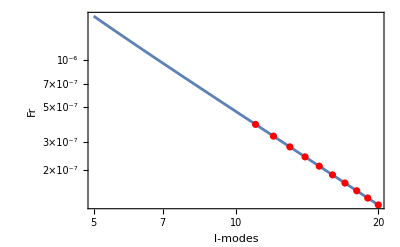

```mathematica
Show[LogLogPlot[fit[l],{l,5,20},Frame->True,FrameLabel->{Style["l-modes",20,FontFamily->"Latin Modern Roman"],Style["Fr",20,FontFamily->"Latin Modern Roman"]}],

ListLogLogPlot[RadiusFrLTab[[2]][[ lmax+2-nbar;;lmax+1]], PlotStyle->Red]
, ImageSize->400]
```

The value of  n̄  varies from a minimum value nbarmin to a maximum value nbarmax.  For a given N ∈ {3,4,5} we considered a weighted average of the values obtained for F_r^self as we vary n̄ from nbarmin to nbarmax, where the weighting for each term is given by the square of the inverse of the fractional diﬀerence in the value of F_r^self as we increase n̄ by one.

Define input parameters

```mathematica
nbarmin =10; 
nbarmax= 15;
If[nbarmax>=lmax, Print["ERROR: nbarmax>=lmax"]];
```

Example

```mathematica
nbar=5;
lmax=20;
NN=3;
FrLTail[nbar,lmax,NN]
```

2.399231787671910912464505×10^-6

```mathematica
NN=3; 

WeightedAvarageN3={NN,RadiusFrLTab[[1]],Sum[(FrWithoutTail+FrLTail[nbar+1,lmax,NN]-FrWithoutTail-FrLTail[nbar,lmax,NN])/(FrWithoutTail+FrLTail[nbar,lmax,NN])*(FrWithoutTail+FrLTail[nbar+1,lmax,NN]),{nbar,nbarmin,nbarmax-1}]/Sum[(FrWithoutTail+FrLTail[nbar+1,lmax,NN]-FrWithoutTail-FrLTail[nbar,lmax,NN])/(FrWithoutTail+FrLTail[nbar,lmax,NN]),{nbar,nbarmin,nbarmax-1}]};
```

```mathematica
NN=4; 

WeightedAvarageN4={NN,RadiusFrLTab[[1]],Sum[(FrWithoutTail+FrLTail[nbar+1,lmax,NN]-FrWithoutTail-FrLTail[nbar,lmax,NN])/(FrWithoutTail+FrLTail[nbar,lmax,NN])*(FrWithoutTail+FrLTail[nbar+1,lmax,NN]),{nbar,nbarmin,nbarmax-1}]/Sum[(FrWithoutTail+FrLTail[nbar+1,lmax,NN]-FrWithoutTail-FrLTail[nbar,lmax,NN])/(FrWithoutTail+FrLTail[nbar,lmax,NN]),{nbar,nbarmin,nbarmax-1}]};
```

```mathematica
NN=5; 

WeightedAvarageN5={NN,RadiusFrLTab[[1]],Sum[(FrWithoutTail+FrLTail[nbar+1,lmax,NN]-FrWithoutTail-FrLTail[nbar,lmax,NN])/(FrWithoutTail+FrLTail[nbar,lmax,NN])*(FrWithoutTail+FrLTail[nbar+1,lmax,NN]),{nbar,nbarmin,nbarmax-1}]/Sum[(FrWithoutTail+FrLTail[nbar+1,lmax,NN]-FrWithoutTail-FrLTail[nbar,lmax,NN])/(FrWithoutTail+FrLTail[nbar,lmax,NN]),{nbar,nbarmin,nbarmax-1}]};
```

```mathematica
WeightedAvarageN3
WeightedAvarageN4
WeightedAvarageN5
```

{3,14.,2.721591593705769×10^-6}

{4,14.,2.7203445098346×10^-6}

{5,14.,2.7199252347111×10^-6}

```mathematica
Fr = (WeightedAvarageN3[[3]]+WeightedAvarageN4[[3]]+WeightedAvarageN5[[3]])/3//N
```

2.72062×10^-6

```mathematica
error = Sqrt[Variance[{WeightedAvarageN3[[3]],WeightedAvarageN4[[3]],WeightedAvarageN5[[3]]}]]
```

8.6677199135×10^-10

```mathematica
Fr+error 
Fr-error
```

2.72149×10^-6

2.71975×10^-6

As a comparison, from https://arxiv.org/pdf/1003.1860:  2.720083e−6

#### Method following XXX. Analytic coefficients computed in https://arxiv.org/pdf/1204.0794, available https://github.com/BlackHolePerturbationToolkit/RegularizationParameters

High-l tail contribution F_r^(l>lmax) = ∑_(l=lmax+1)^∞ F_r^((reg)l) is computed by extrapolating the last n̄  computed l-modes using the fitting formula F_r^((reg)l) = ∑_(n=1)^N (D_(2n)^r)/(∏_(k=1)^n (2L -2k)(2L+2k)). 
nbar: number of l-modes considered for the extrapolation.
N: number of coefficients considered for the fit . x in the implementation varies from 1 to N in the product 
n: nth coefficients

```mathematica
DCoeff[nbar_,n_,N_]:=Numerator[Fit[RadiusFrLTab[[2]][[ lmax+2-nbar;;lmax+1]],Table[1/Product[(2 l+1 -2k) (2 l+1 +2k),{k,1,x}],{x,1,N}],l][[n]]];

FrLTail[nbar_,lmax_,N_] := Sum[(DCoeff[nbar,n,N] (-4)^-n π (-1)^(lmax+1)(lmax+1))/((2n-1)Gamma[n-lmax-1/2]Gamma[n+lmax+3/2]),{n,1,N}];
```

```mathematica
DCoeff[5,1,6]
```

0.00020051821046594813983203283

```mathematica
(*check with the previous example: 2.3992317876*^-6*)
nbar=5;
lmax=20;
NN=3;
FrLTail[nbar,lmax,NN]
```

2.399224319362287372347474×10^-6

```mathematica
NN=6;
```

```mathematica
fit[l_]=Fit[RadiusFrLTab[[2]][[ lmax+2-10;;lmax+1]],Table[1/Product[(2 l+1 -2k) (2 l+1 +2k),{k,1,x}],{x,1,NN}],l]
```

0.00020107258140592932942674583/((-1+2 l) (3+2 l))+0.0018192612470797154883413643/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))+0.032464446150701167523225014/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l))+1.022354996683804505955202/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l))+59.161103092918288892034702/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l))+8787.0546517721196998468861/((-11+2 l) (-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) (13+2 l))

Adding the known regularization  parameters to the fitting formula (F_a[2] = D_a[2] etc)

```mathematica
M=1;
E0=(1-2 M/r0)√(r0/(r0-3M));
L=r0 √(M/(r0-3M)); 
ur=0;
```

#### F_a[2]

```mathematica
D2=((-8 E0^4 (L-r0) r0^10 (L+r0)+4 E0^2 r0^3 (L^2+r0^2) (9 L^6 M+26 L^4 M r0^2+23 L^2 M r0^4+L^2 r0^5+14 M r0^6-3 r0^7)+(2 M-r0) (L^2+r0^2)^2 (28 L^6 M+82 L^4 M r0^2+82 L^2 M r0^4-L^2 r0^5+32 M r0^6-3 r0^7)) EllipticE[L^2/(L^2+r0^2)]+(E0^4 r0^10 (3 L^2-5 r0^2)-E0^2 r0^5 (L^2+r0^2) (18 L^4 M+34 L^2 M r0^2+L^2 r0^3+32 M r0^4-7 r0^5)-(2 M-r0) r0^2 (L^2+r0^2)^2 (14 L^4 M+28 L^2 M r0^2+16 M r0^4-r0^5)) EllipticK[L^2/(L^2+r0^2)])/(2 (-1+2 l) (3+2 l) π r0^6 (-2 M+r0) (L^2+r0^2)^(7/2));
```

#### F_a[4]

```mathematica
D4=(3 ((30 E0^6 r0^19 (23 L^4-82 L^2 r0^2+23 r0^4)-E0^4 r0^8 (L^2+r0^2) (89600 L^12 M+438272 L^10 M r0^2+856504 L^8 M r0^4+837552 L^6 M r0^6+411938 L^4 M r0^8+495 L^4 r0^9+92836 L^2 M r0^10-3690 L^2 r0^11-902 M r0^12+1575 r0^13)+8 E0^2 r0^3 (L^2+r0^2)^2 (5120 L^14 M^2-35200 L^12 M^2 r0^2+26720 L^12 M r0^3-227368 L^10 M^2 r0^4+123200 L^10 M r0^5-456300 L^8 M^2 r0^6+225979 L^8 M r0^7-434510 L^6 M^2 r0^8+206277 L^6 M r0^9-203983 L^4 M^2 r0^10+94211 L^4 M r0^11-40376 L^2 M^2 r0^12+18367 L^2 M r0^13-135 L^2 r0^14-571 M^2 r0^14-146 M r0^15+135 r0^16)+(2 M-r0) (L^2+r0^2)^3 (40960 L^14 M^2-86016 L^12 M^2 r0^2+116480 L^12 M r0^3-860224 L^10 M^2 r0^4+510080 L^10 M r0^5-1780112 L^8 M^2 r0^6+882400 L^8 M r0^7-1657392 L^6 M^2 r0^8+752340 L^6 M r0^9-743164 L^4 M^2 r0^10+316100 L^4 M r0^11+30 L^4 r0^12-136236 L^2 M^2 r0^12+53200 L^2 M r0^13+75 L^2 r0^14-3120 M^2 r0^14+160 M r0^15+165 r0^16)) EllipticE[L^2/(L^2+r0^2)]+(-15 E0^6 r0^19 (15 L^4-82 L^2 r0^2+31 r0^4)+E0^4 r0^10 (L^2+r0^2) (44800 L^10 M+179936 L^8 M r0^2+272908 L^6 M r0^4+187126 L^4 M r0^6+135 L^4 r0^7+55232 L^2 M r0^8-1710 L^2 r0^9+118 M r0^10+1035 r0^11)-(2 M-r0) r0^2 (L^2+r0^2)^3 (20480 L^12 M^2-60928 L^10 M^2 r0^2+58240 L^10 M r0^3-375840 L^8 M^2 r0^4+204080 L^8 M r0^5-564472 L^6 M^2 r0^6+265360 L^6 M r0^7-350956 L^4 M^2 r0^8+152380 L^4 M r0^9-84276 L^2 M^2 r0^10+33740 L^2 M r0^11+15 L^2 r0^12-3120 M^2 r0^12+640 M r0^13+75 r0^14)-E0^2 r0^5 (L^2+r0^2)^2 (20480 L^12 M^2-158720 L^10 M^2 r0^2+106880 L^10 M r0^3-769632 L^8 M^2 r0^4+399280 L^8 M r0^5-1159632 L^6 M^2 r0^6+559556 L^6 M r0^7-755876 L^4 M^2 r0^8+352004 L^4 M r0^9-196524 L^2 M^2 r0^10+89680 L^2 M r0^11-405 L^2 r0^12-5528 M^2 r0^12+512 M r0^13+675 r0^14)) EllipticK[L^2/(L^2+r0^2)]))/(40 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π r0^13 (-2 M+r0) (L^2+r0^2)^(11/2));
```

#### F_a[6]

```mathematica
D6=(-1800 √2)/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l))(((11550720000 L^28 M^4-10936320000 L^28 M^3 r0+737280 L^26 M^2 (3500 L^2+127167 M^2) r0^2+122880 (-639361+79800 E0^2) L^26 M^3 r0^3-4096 L^24 M^2 (150 (-18471+7480 E0^2) L^2-73805219 M^2) r0^4+2048 L^24 M (1097250 L^2+(-89756449+32656620 E0^2) M^2) r0^5+640 L^22 M^2 (16 (-2809627-2053380 E0^2+196800 E0^4) L^2+625211897 M^2) r0^6-64 L^22 M (84000 (-4195+894 E0^2) L^2-(1348765243+2439064160 E0^2) M^2) r0^7+64 L^20 M^2 ((-5439619239+343826592 E0^2+158518400 E0^4) L^2-3908647817 M^2) r0^8+32 L^20 M (875 (3659665-1583232 E0^2+104448 E0^4) L^2+(46847905117+296613362 E0^2) M^2) r0^9+32 L^18 M^2 ((-38854641925+12153454906 E0^2+184100608 E0^4) L^2-60045997176 M^2) r0^10-16 L^18 M (175 (-99342933+65453006 E0^2-8798208 E0^4+143360 E0^6) L^2+2 (-127875992679+23557526987 E0^2) M^2) r0^11-16 L^16 M^2 ((160486523791-82029572466 E0^2+4764133676 E0^4) L^2+229746433995 M^2) r0^12-8 L^16 M (100 (-626335297+558738416 E0^2-114713672 E0^4+3850240 E0^6) L^2+(-791307530801+243102521314 E0^2) M^2) r0^13-8 L^14 M^2 ((437966473103-304819503332 E0^2+33667035676 E0^4) L^2+514668450240 M^2) r0^14-8 L^14 M (50 (-1571859247+1779736425 E0^2-495520816 E0^4+25608640 E0^6) L^2+(-804714380459+331443494684 E0^2) M^2) r0^15-8 L^12 M^2 ((413867836807-362527040154 E0^2+56947729671 E0^4) L^2+379165247618 M^2) r0^16+2 L^12 M (-25 (-11214221011+15461994934 E0^2-5461026466 E0^4+383783424 E0^6) L^2+4 (559966213873-284315434978 E0^2) M^2) r0^17-4 L^10 (1750 L^4+(548115649114-576771534874 E0^2+115704920389 E0^4) L^2 M^2+374852529720 M^4) r0^18+2 L^10 M (-25 (-7109284497+11586327644 E0^2-4961589157 E0^4+438774310 E0^6) L^2+52 (20472918763-12187587628 E0^2) M^2) r0^19-L^8 (875 (61+2 E0^2) L^4+4 (251025534014-306573662228 E0^2+73614363957 E0^4) L^2 M^2+483945880272 M^4) r0^20-2 L^8 M (25 (-3143635831+5909703846 E0^2-2956043094 E0^4+306811838 E0^6) L^2+28 (-11907014833+7953917234 E0^2) M^2) r0^21+L^6 (875 (-198+16 E0^2+9 E0^4) L^4-8 (38140673807-52259644437 E0^2+14137813862 E0^4) L^2 M^2-93788994240 M^4) r0^22+2 L^6 M (-25 (-927168557+1960667516 E0^2-1098582897 E0^4+120153142 E0^6) L^2+4 (15751988521-11050793524 E0^2) M^2) r0^23-(875 (403+898 E0^2+1599 E0^4+290 E0^6) L^8+8 (7025397453-10237387702 E0^2+2791229516 E0^4) L^6 M^2+8708359984 L^4 M^4) r0^24-2 L^4 M (25 (-166444761+380607490 E0^2-220305958 E0^4+17066212 E0^6) L^2+4 (-1435407943+831043694 E0^2) M^2) r0^25+2 (875 (-286-1128 E0^2+789 E0^4+2044 E0^6+176 E0^8) L^6-2 (1258803094-1620462718 E0^2+187417037 E0^4) L^4 M^2-34884592 L^2 M^4) r0^26+2 L^2 M (25 (14725291-32063604 E0^2+12033991 E0^4+4193382 E0^6) L^2+4 (14772489+50021432 E0^2) M^2) r0^27-(875 (531+1190 E0^2-6738 E0^4+2124 E0^6+2720 E0^8) L^4+4 (17156590+57322108 E0^2-91292731 E0^4) L^2 M^2-20634368 M^4) r0^28+2 M (25 (279517+295006 E0^2-2223838 E0^4+1640050 E0^6) L^2+16 (-648221+1274962 E0^2) M^2) r0^29+(875 (-278+704 E0^2+2301 E0^4-5384 E0^6+2720 E0^8) L^2+8 (695018-2748205 E0^2+2096867 E0^4) M^2) r0^30+50 (-1337+5540 E0^2-10909 E0^4+6086 E0^6) M r0^31-875 (61-554 E0^2+1251 E0^4-1118 E0^6+352 E0^8) r0^32) EllipticE[L^2/(L^2+r0^2)])/(336000 √2 π r0^18 (-2 M+r0) (L^2+r0^2)^(15/2))+((-5775360000 L^26 M^4+5468160000 L^26 M^3 r0-491520 L^24 M^2 (2625 L^2+85094 M^2) r0^2-368640 (-93581+13300 E0^2) L^24 M^3 r0^3+1024 L^22 M^2 (1200 (-3699+1870 E0^2) L^2-112135333 M^2) r0^4-512 L^22 M (2194500 L^2+(-121057493+56934240 E0^2) M^2) r0^5-128 L^20 M^2 (20 (-7149209-3321360 E0^2+393600 E0^4) L^2+792474019 M^2) r0^6+640 L^20 M (1050 (-15317+3576 E0^2) L^2-(149827039+82458340 E0^2) M^2) r0^7-64 L^18 M^2 ((-2466671642+286477896 E0^2+65483200 E0^4) L^2-3269396747 M^2) r0^8-16 L^18 M (875 (3020113-1433040 E0^2+104448 E0^4) L^2+(41462584535-2510311428 E0^2) M^2) r0^9+8 L^16 M^2 ((60559582341-22257634640 E0^2+84277184 E0^4) L^2+96850468006 M^2) r0^10+8 L^16 M (350 (-36622559+26497183 E0^2-3942144 E0^4+71680 E0^6) L^2+(-183867893311+42480334390 E0^2) M^2) r0^11+16 L^14 M^2 ((54184774577-31340000896 E0^2+2334208970 E0^4) L^2+73178097941 M^2) r0^12+8 L^14 M (50 (-406482195+398671047 E0^2-90739400 E0^4+3411200 E0^6) L^2+(-238349144243+84713577429 E0^2) M^2) r0^13+4 L^12 M^2 ((253248403327-197101634262 E0^2+25523739942 E0^4) L^2+266423719064 M^2) r0^14+2 L^12 M (25 (-3523094281+4390137912 E0^2-1356655832 E0^4+78744320 E0^6) L^2+4 (-200899023519+93432910267 E0^2) M^2) r0^15+4 L^10 M^2 ((200373875828-195093313467 E0^2+35038312341 E0^4) L^2+156482597680 M^2) r0^16+2 L^10 M (25 (-2643231423+4013032889 E0^2-1573282069 E0^4+124187312 E0^6) L^2+4 (-112451860211+63595775022 E0^2) M^2) r0^17+4 L^8 (875 L^4+(107302641991-124824930971 E0^2+28207483751 E0^4) L^2 M^2+58809801532 M^4) r0^18+2 L^8 M (25 (-1358858193+2436723165 E0^2-1155242046 E0^4+113901787 E0^6) L^2+4 (-40812722065+26651789876 E0^2) M^2) r0^19+L^6 (875 (27+E0^2) L^4+16 (9406935758-12581869215 E0^2+3337159007 E0^4) L^2 M^2+52697608528 M^4) r0^20+2 L^6 M (25 (-460702319+948766698 E0^2-520130679 E0^4+58233110 E0^6) L^2+12 (-2962402147+2098304315 E0^2) M^2) r0^21+(875 (99+413 E0^2+558 E0^4+75 E0^6) L^8+4 (7959650533-11640361404 E0^2+3292605820 E0^4) L^6 M^2+5751437056 L^4 M^4) r0^22+2 L^4 M (25 (-94648995+215633266 E0^2-127399500 E0^4+12711802 E0^6) L^2+4 (-947387093+606804899 E0^2) M^2) r0^23+(-875 (-206-874 E0^2+1320 E0^4+1700 E0^6+105 E0^8) L^6+4 (829281052-1148410867 E0^2+217789077 E0^4) L^4 M^2+95125728 L^2 M^4) r0^24-2 L^2 M (25 (9662541-22015677 E0^2+10337027 E0^4+1281624 E0^6) L^2+4 (16814851+22690668 E0^2) M^2) r0^25+(875 (234+154 E0^2-3468 E0^4+1746 E0^6+1189 E0^8) L^4+4 (16426443+22694013 E0^2-50089769 E0^4) L^2 M^2-15043328 M^4) r0^26-2 M (25 (227003-17409 E0^2-1174946 E0^4+956397 E0^6) L^2+176 (-45031+88682 E0^2) M^2) r0^27-(875 (-135+667 E0^2+744 E0^4-2748 E0^6+1531 E0^8) L^2+8 (595478-2277805 E0^2+1726007 E0^4) M^2) r0^28-50 (-4907+19400 E0^2-27919 E0^4+12806 E0^6) M r0^29+875 (31-359 E0^2+846 E0^4-773 E0^6+247 E0^8) r0^30) EllipticK[L^2/(L^2+r0^2)])/(336000 √2 π r0^16 (-2 M+r0) (L^2+r0^2)^(15/2)));
```

#### Building the new interpolating function

```mathematica
NN=6
```

6

```mathematica
DCoeff[nbar_, n_, NN_] := Block[{dcoeff,l,DD},
If[n==1, dcoeff = D2* Product[(2  l + 1 - 2 k)  (2  l + 1 + 2 k), {k, 1, 1}],
If[n==2, dcoeff = D4*Product[(2  l + 1 - 2 k)  (2  l + 1 + 2 k), {k, 1, 2}],
If[n==3, dcoeff = D6*Product[(2  l + 1 - 2 k)  (2  l + 1 + 2 k), {k, 1, 3}],
dcoeff = FindFit[RadiusFrLTab[[2]][[ lmax + 2 - nbar ;; lmax + 1]], D2 + D4 + D6 + Sum[DD[2 x]/Product[(2  l + 1 - 2 k)  (2  l + 1 + 2 k), {k, 1, x}], {x, 4, NN}], Table[DD[2 nn ],{nn,4, NN}], l][[n-3, 2]];
];
];
];
Return[dcoeff]];
```

```mathematica
DCoeff[5, 1, 6]
DCoeff[5, 2, 6] 
DCoeff[5, 3, 6] 
DCoeff[5, 4, 6] 
DCoeff[5, 5, 6] 
DCoeff[5, 6, 6]
```

0.0002010725712759107475532349367988974591810080306

0.00181930621291856113171159393595444068673802921

0.0323945738632593606437251874333675752284490958

1.06452372459736247048408602

54.260780640284347621303592

6524.36086887968643901018225

```mathematica
FrLTail[nbar_,lmax_,NN_] := Sum[(DCoeff[nbar,n,NN] (-4)^-n π (-1)^(lmax+1)(lmax+1))/((2n-1)Gamma[n-lmax-1/2]Gamma[n+lmax+3/2]),{n,1,NN}];
```

```mathematica
(*check with the previous examples: 1)2.3992317876*^-6, 2)2.39922431936*^-6*)
nbar=5;
lmax=20;
NN=3;
N[FrLTail[nbar,lmax,NN],20]
```

2.3992201187201650852×10^-6

```mathematica
nbarmin
nbarmax
FrWithoutTail
FrLTail[nbarmin+1,lmax,3]
```

10

15

3.20863032822449516976×10^-7

2.399220118720165085213647170547050012352329316×10^-6

In this case NN>3 as the fitting formula is fixed for NN<=3.

```mathematica
NN=4; 

WeightedAvarageN4={NN,RadiusFrLTab[[1]],Sum[(FrWithoutTail+FrLTail[nbar+1,lmax,NN]-FrWithoutTail-FrLTail[nbar,lmax,NN])/(FrWithoutTail+FrLTail[nbar,lmax,NN])*(FrWithoutTail+FrLTail[nbar+1,lmax,NN]),{nbar,nbarmin,nbarmax-1}]/Sum[(FrWithoutTail+FrLTail[nbar+1,lmax,NN]-FrWithoutTail-FrLTail[nbar,lmax,NN])/(FrWithoutTail+FrLTail[nbar,lmax,NN]),{nbar,nbarmin,nbarmax-1}]};
```

```mathematica
NN=5; 

WeightedAvarageN5={NN,RadiusFrLTab[[1]],Sum[(FrWithoutTail+FrLTail[nbar+1,lmax,NN]-FrWithoutTail-FrLTail[nbar,lmax,NN])/(FrWithoutTail+FrLTail[nbar,lmax,NN])*(FrWithoutTail+FrLTail[nbar+1,lmax,NN]),{nbar,nbarmin,nbarmax-1}]/Sum[(FrWithoutTail+FrLTail[nbar+1,lmax,NN]-FrWithoutTail-FrLTail[nbar,lmax,NN])/(FrWithoutTail+FrLTail[nbar,lmax,NN]),{nbar,nbarmin,nbarmax-1}]};
```

```mathematica
NN=6; 

WeightedAvarageN6={NN,RadiusFrLTab[[1]],Sum[(FrWithoutTail+FrLTail[nbar+1,lmax,NN]-FrWithoutTail-FrLTail[nbar,lmax,NN])/(FrWithoutTail+FrLTail[nbar,lmax,NN])*(FrWithoutTail+FrLTail[nbar+1,lmax,NN]),{nbar,nbarmin,nbarmax-1}]/Sum[(FrWithoutTail+FrLTail[nbar+1,lmax,NN]-FrWithoutTail-FrLTail[nbar,lmax,NN])/(FrWithoutTail+FrLTail[nbar,lmax,NN]),{nbar,nbarmin,nbarmax-1}]};
```

```mathematica
WeightedAvarageN4
WeightedAvarageN5
WeightedAvarageN6
```

{4,14.,2.720083645763×10^-6}

{5,14.,2.720083672175×10^-6}

{6,14.,2.720083621194×10^-6}

```mathematica
Fr = (WeightedAvarageN4[[3]]+WeightedAvarageN5[[3]]+WeightedAvarageN6[[3]])/3
```

2.720083646377×10^-6

```mathematica
error = Sqrt[Variance[{WeightedAvarageN4[[3]],WeightedAvarageN5[[3]],WeightedAvarageN6[[3]]}]]
```

2.55×10^-14

```mathematica
Fr+error 
Fr-error
```

2.72008367187×10^-6

2.72008362088×10^-6

As a comparison, from https://arxiv.org/pdf/1003.1860:  2.720083e−6

Related Guides

Teukolsky

Related Tech Notes

## Metadata

### Categorization

Tech Note

ToolkitHackaton

ToolkitHackaton/tutorial/ScalarSelfForceTutorial

### Keywords